# Optimization of the time-averaged excess work in STIRAP

## Parameters and definitions

```mathematica
ℏ = 1
ti = 0
Δ= 0.1
(*Boundary conditions for the protocols*)
Ωpi = 10.0
Ωpf = 0.1
(*Range of the protocol time*)
Tmin = 0.1
Tmax = 30.1
(*Sample size*)
m = 9
ΔT = (Tmax-Tmin)/m
(*Protocols*)
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
(*Initial conditions - |n0 >*)
(*c10 = Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
c20 = 0
c30 = -Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]*)
(*Initial conditions - |n- >*)
ϕ0 = 0.5*ArcTan[Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]/Δ]
c10 = (Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ0]
c20 = -Sin[ϕ0]
c30 = (Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ0]
(*Final state in adiabatic evolution*)
ϕf = 0.5*ArcTan[Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ]/Δ]
c1f = (Ωp[tf,tf]/Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ])*Cos[ϕf]
c2f = -Sin[ϕf]
c3f = (Ωs[tf]/Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ])*Cos[ϕf]
(*Counterdiabatic driving for the linear protocol*)
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
(*Energetic costs*)
Cost[Ωp_,Ωs_,Ωa_,Δ_,tf_] := NIntegrate[√(Δ^2 ℏ^2+(Ωa^2 ℏ^2)/2+(Ωp^2 ℏ^2)/2+(Ωs^2 ℏ^2)/2),{t,ti,tf}]/tf
Wex[c1_,c2_,c3_,Ωp_,Ωs_,Δ_] := ℏ*(Ωp*Re[c1*Conjugate[c2]] + Ωs*Re[c2*Conjugate[c3]]+ 2*Δ*Abs[c2]^2)
(*Sample points*)
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

1

0

0.1

10.

0.1

0.1

30.1

9

3.33333

0.780423

0.707089

-0.70358

0.0707089

0.73581

0.0737609

-0.671187

0.737609

{0.0454959,1.56203,3.07856,4.59509,6.11162,7.62815,9.14468,10.6612,12.1777,13.6943}

```mathematica
(*Minimum fidelity*)
Fmin = Abs[c10*c1f + c20*c2f + c30*c3f]
```

0.576545

## Linear protocol

The linear protocol and the variation of the eigenvalues

1.

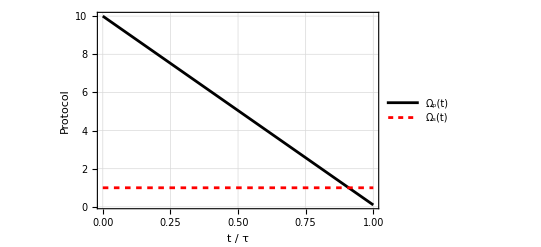

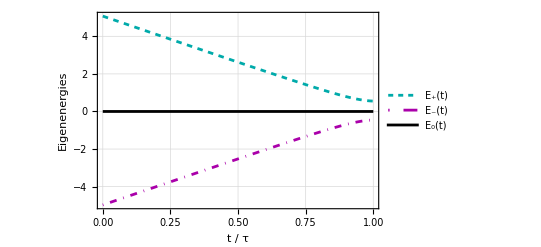

-Graphics-

```mathematica
tf = 1.0
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], Dashing[0.01]},FrameLabel ->{"t / τ", "Eigenenergies"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Magenta], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.78}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Black],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

Solution of the Schrödinger equation for the linear protocol

```mathematica
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==c10,c2[ti]==c20,c3[ti]==c30 },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

```mathematica
(*Fidelity*)
FLIN = Table[Abs[(c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
```

{0.57699,0.694997,0.757162,0.795823,0.825816,0.850383,0.869089,0.885121,0.898852,0.90986}

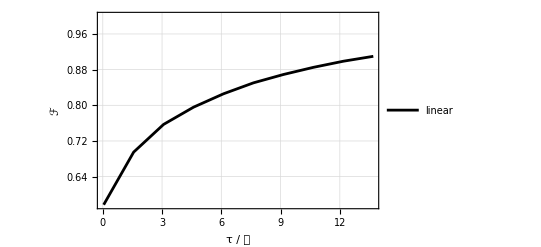

```mathematica
(*Fidelity*)
gLIN = ListPlot[Transpose[{time,FLIN}], Joined->True,PlotStyle->{Black}, PlotRange->{Fmin,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.10}]]
```

## Minimal action

The protocols of the minimal action (MA) method comes from the minimization of the adiabatic action.

```mathematica
(*Transitions between n- and n0*)
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between n- and n+*)
ProtMA3 = Table[NDSolve[{D[ΩpMA3'[t]/(ΩpMA3[t]^2 + Ωs[t]^2),t] ==0 , ΩpMA3[ti]==Ωpi, ΩpMA3[tf]==Ωpf},ΩpMA3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

{{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}}}

5

13.4333

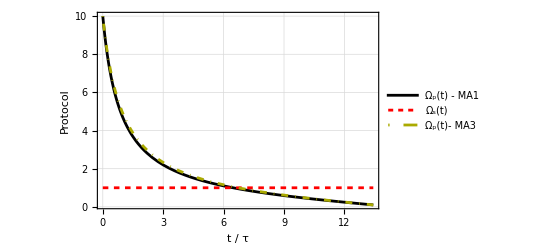

```mathematica
(*Protocol time for the Figure*)
n = 5
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - MA1",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.78}]],Plot[Evaluate[ΩpMA3[t]/.Flatten[Part[ProtMA3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Yellow], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)- MA3",10]},LegendLayout->"Row"],{Right,0.86}]]]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==c10,c2MA[ti]==c20,c3MA[ti]==c30 },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

```mathematica
(*Fidelity*)
FMA = Table[Abs[(c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
```

{0.576779,0.789753,0.952069,0.97136,0.988904,0.990323,0.995072,0.995263,0.997137,0.997248}

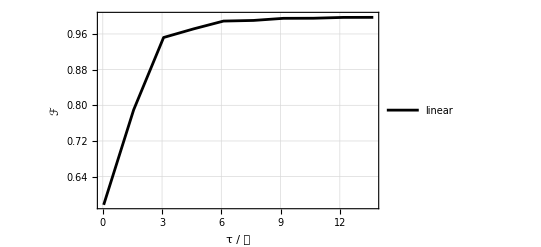

```mathematica
(*Fidelity*)
gMA = ListPlot[Transpose[{time,FMA}], Joined->True,PlotStyle->{Black}, PlotRange->{Fmin,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.10}]]
```

## Fast quasidiabatic

The protocols for the fast quasidiabatic method (FQ) can be found by solving the EDO generated when we make the adiabatic quantitative condition constant.

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
ProtFQ3 = Table[DSolve[{D[ΩpFQ3[t]*ΩpFQ3'[t]/(ΩpFQ3[t]^2 + Ωs[t]^2)^(4/2),t] ==0 , ΩpFQ3[ti]==Ωpi, ΩpFQ3[tf]==Ωpf},ΩpFQ3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

General::stop: Further output of DSolve::bvnul will be suppressed during this calculation.

{{{ΩpFQ3→Function[{t},0.707107 √((0.990099-9.80198 t)/(0.0049505+4.90099 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.285495 t)/(0.0049505+0.142747 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.144857 t)/(0.0049505+0.0724284 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0970493 t)/(0.0049505+0.0485247 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0729676 t)/(0.0049505+0.0364838 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0584611 t)/(0.0049505+0.0292306 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0487661 t)/(0.0049505+0.024383 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0418292 t)/(0.0049505+0.0209146 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0366201 t)/(0.0049505+0.0183101 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.990099-0.0325647 t)/(0.0049505+0.0162824 t))]}}}

Protocols for the fast quasidiabatic method.

1

0.1

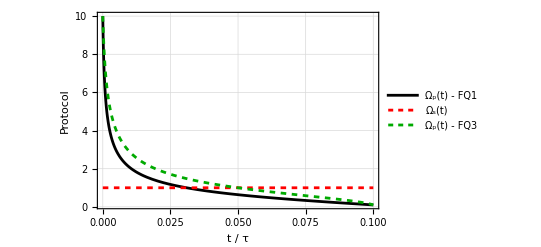

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ1",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.78}]],Plot[Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green],Dashing[0.01]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ3",10]},LegendLayout->"Row"],{Right,0.86}]]]
```

Solution of the Schrödinger equation for the fast quasidiabatic protocol.

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==c10,c2FQ[ti]==c20,c3FQ[ti]==c30 },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolFQ3 = Table[NDSolve[{ⅈ*ℏ*c1FQ3'[t] ==(ℏ/2)*Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3,(tf-Tmin)/ΔT + 1]]]*c2FQ3[t],ⅈ*ℏ*c2FQ3'[t] ==(ℏ/2)*Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3,(tf-Tmin)/ΔT + 1]]]*c1FQ3[t]+(ℏ)*Δ*c2FQ3[t]+ (ℏ/2)*Ωs[t]*c3FQ3[t],ⅈ*ℏ*c3FQ3'[t] ==+(ℏ/2)*Ωs[t]*c2FQ3[t],c1FQ3[ti]==c10,c2FQ3[ti]==c20,c3FQ3[ti]==c30 },{c1FQ3,c2FQ3,c3FQ3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

{{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}},{{c1FQ3→InterpolatingFunction[…],c2FQ3→InterpolatingFunction[…],c3FQ3→InterpolatingFunction[…]}}}

```mathematica
(*Fidelity*)
FFQ = Table[Abs[(c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
FFQ3 = Table[Abs[(c1FQ3[t]/.Part[Flatten[Part[SolFQ3,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2FQ3[t]/.Part[Flatten[Part[SolFQ3,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3FQ3[t]/.Part[Flatten[Part[SolFQ3,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
```

{0.576719,0.752027,0.972263,0.991134,0.978373,0.998648,0.99442,0.994133,0.999978,0.996081}

{0.576824,0.826675,0.975472,0.948991,0.986551,0.974905,0.989242,0.985799,0.990446,0.991434}

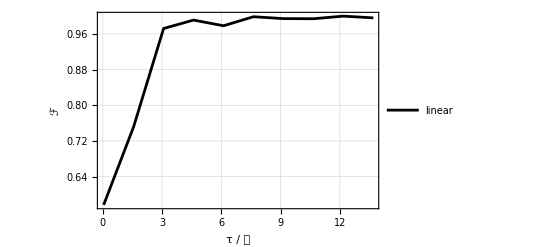

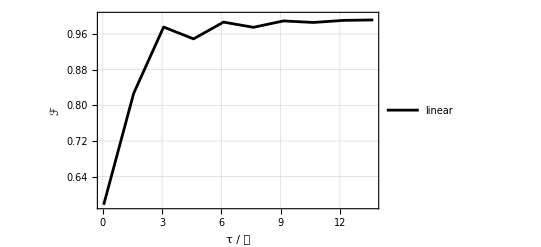

```mathematica
(*Fidelity*)
gFQ = ListPlot[Transpose[{time,FFQ}], Joined->True,PlotStyle->{Black}, PlotRange->{Fmin,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.10}]]
gFQ3 = ListPlot[Transpose[{time,FFQ3}], Joined->True,PlotStyle->{Black}, PlotRange->{Fmin,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.10}]]
```

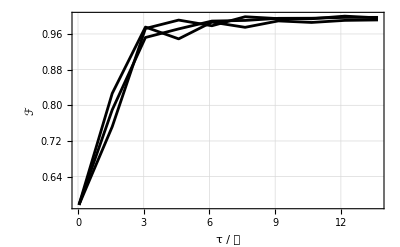

```mathematica
Show[gFQ,gMA ,gFQ3]
```

## Optimal time-averaged excess work

Apparently, the protocol found by optimizing the time-averaged excess work is equal to de fast quasidiabatic protocol. The protocols can be found by using the Euler-Lagrange equations on the excess work. The solutions are given below.

```mathematica
ProtOP = Table[NDSolve[{(1+ΩpOP[t]^2) (1+3 ΩpOP[t]^2+3 ΩpOP[t]^4+ΩpOP[t]^6-12 ΩpOP'[t]^2) (-3 ΩpOP[t] ΩpOP'[t]^2+ΩpOP''[t]+ΩpOP[t]^2 ΩpOP''[t])==0, ΩpOP[ti]==Ωpi, ΩpOP[tf]==Ωpf},ΩpOP[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}}}

Protocol found by minimizing the time-averaged excess work.

1

0.1

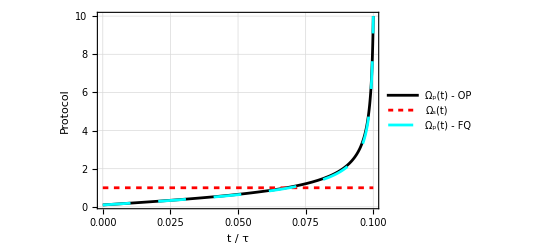

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpOP[t]/.Flatten[Part[ProtOP, n]]],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - OP",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Cyan, Dashing[0.05]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ",10]},LegendLayout->"Row"],{Left,0.86}]]]
```